# Figures for DG notes

Spring 2025

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{newtx,exscale}"},FontSize->16];
```

```mathematica
ColorMapSuitePath=NotebookDirectory[]<>"/ScientificColourMaps7";
ColorMapSuite[name_String]:=ColorMapSuite[name,-1]
ColorMapSuite[name_String,el_]:=With[{list=Transpose@{Subdivide[0,1,255],RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]}},Blend[list,{##}[[el]]]&]
ColorMapSuiteCategorical[name_String]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/CategoricalPalettes/"<>name<>"S.mat"];
ColorMapSuiteDiscrete[name_String,n_]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/DiscretePalettes/"<>name<>IntegerString[n]<>".mat"];
cols=ColorMapSuiteCategorical["batlow"];
```

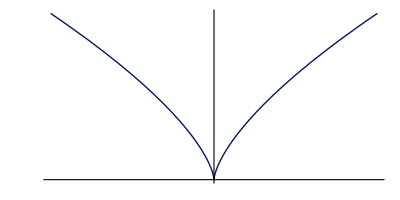

```mathematica
cusp=ParametricPlot[{t^3,t^2}, {t,-1,1},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-1,1}],Table[{i,MaTeX[i]},{i,0,1}]}]
```

```mathematica
Export[NotebookDirectory[]<>"cusp.pdf",cusp]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/cusp.pdf

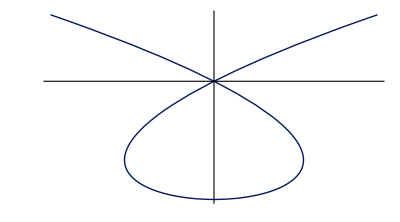

```mathematica
α[t_]:={t^3-4t,t^2-4};
conic=ParametricPlot[α[t], {t,-2.5,2.5},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-6,6,2}],Table[{i,MaTeX[i]},{i,-4,2,2}]}]
```

```mathematica
Export[NotebookDirectory[]<>"conic.pdf",conic]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/conic.pdf

```mathematica
D[{√(1-z^2)Cos[θ],√(1-z^2)Sin[θ],z},θ]
```

{-√(1-z^2) Sin[θ],√(1-z^2) Cos[θ],0}

```mathematica
D[{√(1-z^2)Cos[θ],√(1-z^2)Sin[θ],z},z]
```

{-(z Cos[θ])/(√(1-z^2)),-(z Sin[θ])/(√(1-z^2)),1}

```mathematica
dtheta=With[{zstep=.1,θstep=2π/15},
Graphics3D[{cols[[5]],Arrowheads[.02],Table[Arrow[Tube[{#,#+.35Sqrt[1-z^2]{-Sin[θ],Cos[θ],0}},.006]]&[{Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z}],{z,-1+zstep,1-zstep,zstep},{θ,0,2π-θstep,θstep}],White,Opacity[.7],Sphere[]},PlotRange->1.4,ImageSize->800,Lighting->"Neutral",Boxed->False,ViewPoint->{10,0,3},ViewVertical->{0,0,1},SphericalRegion->False,ViewAngle->π/37]
];
```

```mathematica
dtheta
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"dtheta.png",dtheta]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/dtheta.png

```mathematica
dz=With[{zstep=.2,θstep=2π/15},
Graphics3D[{cols[[3]],Arrowheads[.02],Table[Arrow[Tube[{#,#+.35{-(z Cos[θ])/(√(1-z^2)),-(z Sin[θ])/(√(1-z^2)),1}},.006]]&[{Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z}],{z,-1+zstep,1-zstep,zstep},{θ,0,2π-θstep,θstep}],White,Opacity[.7],Sphere[]},PlotRange->1.4,ImageSize->800,Lighting->"Neutral",Boxed->False,ViewPoint->{10,0,3},ViewVertical->{0,0,1},SphericalRegion->False,ViewAngle->π/37]
];
```

```mathematica
dz
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"dz.png",dz]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/dz.png

```mathematica
X[{x_,y_,z_}]:={z x, z y, z^2-1};
```

```mathematica
flowfield=Module[{n=4,m=12,x,y,z},
Graphics3D[{cols[[5]],Thickness[.007],
Table[{x,y,z}={√(1-z^2)Cos[θ+(-1)^(n z)#/n],√(1-z^2)Sin[θ+(-1)^(n z)#/n],z};
Arrow[Tube[{{x,y,z},{x,y,z}+X[{x,y,z}]}]],
{z,-1,1,1/n},{θ,0,2π-#,#}]&[2π/m],
Opacity[.6],White,Sphere[]
},
Boxed->False,ViewPoint->Front,Lighting->"Neutral",ImageSize->800]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"flowfield.png",flowfield]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/flowfield.png

```mathematica
{Subscript[ϕ, 1][t],Subscript[ϕ, 2][t],Subscript[ϕ, 3][t]}/.DSolve[Table[Subscript[ϕ, i]'[t]==X[{Subscript[ϕ, 1][t],Subscript[ϕ, 2][t],Subscript[ϕ, 3][t]}][[i]],{i,1,3}]&&Subscript[ϕ, 1][0]==x&&Subscript[ϕ, 2][0]==y&&Subscript[ϕ, 3][0]==z,{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3]},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{-(2 ⅇ^t x)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(2 ⅇ^t y)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(1-ⅇ^(2 t)+z+ⅇ^(2 t) z)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z)}}

```mathematica
conformalflow=Module[{n=4,m=12,x,y,z},
Show[
Graphics3D[{cols[[5]],Thickness[.007],
Table[{x,y,z}={√(1-z^2)Cos[θ+(-1)^(n z)#/n],√(1-z^2)Sin[θ+(-1)^(n z)#/n],z};
Arrow[Tube[{{x,y,z},{x,y,z}+X[{x,y,z}]}]],
{z,-1,1,1/n},{θ,0,2π-#,#}]&[2π/m],
Opacity[.6],White,Sphere[]
}],
With[{z=0,x=Cos[θ],y=Sin[θ]},
ParametricPlot3D[Table[{-(2 ⅇ^t x)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(2 ⅇ^t y)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(1-ⅇ^(2 t)+z+ⅇ^(2 t) z)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z)},{θ,2 π/(m n),2π-π/m,π/m}],{t,-10,10},PlotStyle->Directive[Thickness[.007],cols[[3]]]]],
Boxed->False,ViewPoint->Front,ViewVertical->{0,0,1},Lighting->"Neutral",ImageSize->800]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"conformalflow.png",conformalflow]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/conformalflow.png

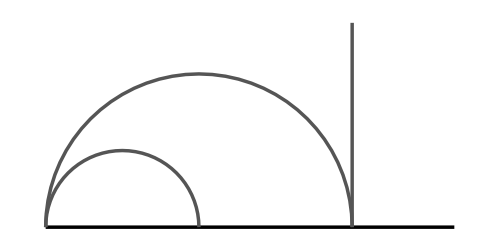

```mathematica
hyperbolicgeodesics=Graphics[{Black,Thickness[.005],Line[{{-1,0},{1,0}}],Darker[Gray],Line[{{1/2,0},{1/2,1}}],Circle[{-5/8,0},3/8,{0,π}],Circle[{-1/4,0},3/4,{0,π}]},ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"hyperbolicgeodesics.pdf",hyperbolicgeodesics]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hyperbolicgeodesics.pdf

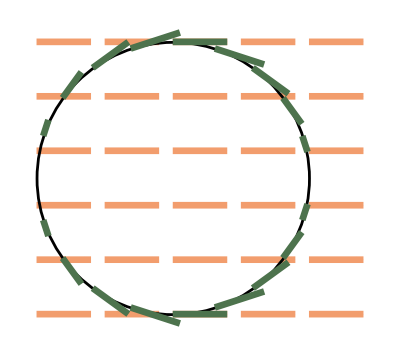

```mathematica
pullbackdx=Graphics[{Thickness[.012],cols[[5]],Table[Arrow[{#,#+.4{1,0}}]&[{x,y}],{y,-1,1,.4},{x,-1,1,.5}],Thickness[.005],Black,Circle[],Thickness[.012],cols[[7]],Table[Arrow[{#,#-.4#[[2]]{-#[[2]],#[[1]]}}]&[ReIm[E^(I θ)]],{θ,0,2π,2π/20}]}]
```

```mathematica
Export[NotebookDirectory[]<>"pullbackdx.pdf",pullbackdx]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/pullbackdx.pdf